```mathematica
SetDirectory[NotebookDirectory[]];
```

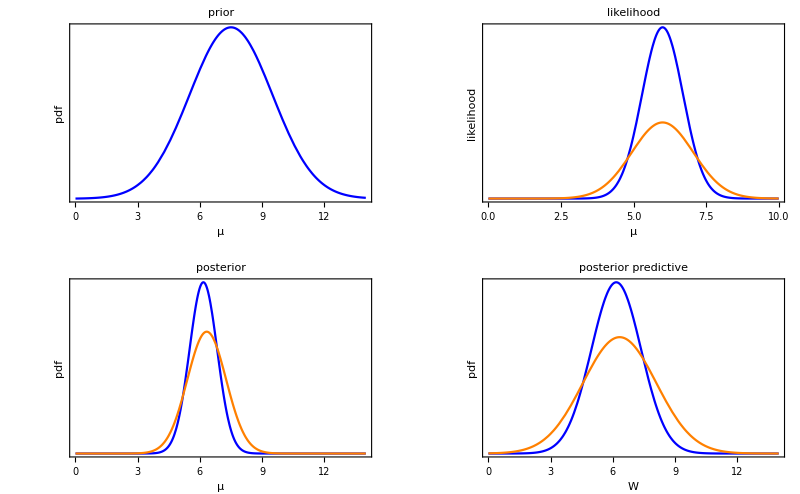

Evaluation_normalPosteriorPredictiveWeight.pdf

```mathematica
n = 2;
xbar = 6;
μ0 = 7.5;
σ0 = 2;
σ1 = 1;
σ2 = 1.5;
gPrior1 = Plot[PDF[NormalDistribution[μ0,σ0],x],{x,0,14},PlotRange->Full,PlotStyle->Blue,BaseStyle->{FontSize->16},Frame->{True,True,False,False},FrameLabel->{"μ","pdf"},FrameTicks->{True,None},PlotLabel->"prior"];
gLikelihood1 = Plot[{Likelihood[NormalDistribution[μ,σ1],ConstantArray[xbar,n]],Likelihood[NormalDistribution[μ,σ2],ConstantArray[xbar,n]]},{μ,0,10},PlotRange->Full,PlotStyle->{Blue,Orange},BaseStyle->{FontSize->16},Frame->{True,True,False,False},FrameLabel->{"μ","likelihood "},FrameTicks->{True,None},PlotLabel->"likelihood"];
gPosterior1 = Plot[{PDF[NormalDistribution[((μ0/(σ0^2)) + (n xbar)/(σ1^2)) / ((1/(σ0^2))+ (n/(σ1^2))), Sqrt[((1/(σ0^2))+ (n/(σ1^2)))^(-1)]],x],PDF[NormalDistribution[((μ0/(σ0^2)) + (n xbar)/(σ2^2)) / ((1/(σ0^2))+ (n/(σ2^2))), Sqrt[((1/(σ0^2))+ (n/(σ2^2)))^(-1)]],x]},{x,0,14},PlotRange->Full,PlotStyle->{Blue,Orange},BaseStyle->{FontSize->16},Frame->{True,True,False,False},FrameLabel->{"μ","pdf"},FrameTicks->{True,None},PlotLabel->"posterior"];
gPosteriorPredictive1 = Plot[{PDF[NormalDistribution[((μ0/(σ0^2)) + (n xbar)/(σ1^2)) / ((1/(σ0^2))+ (n/(σ1^2))),Sqrt[σ1^2+ ((1/(σ0^2))+ (n/(σ1^2)))^(-1)]],x],PDF[NormalDistribution[((μ0/(σ0^2)) + (n xbar)/(σ2^2)) / ((1/(σ0^2))+ (n/(σ2^2))),Sqrt[σ2^2+ ((1/(σ0^2))+ (n/(σ2^2)))^(-1)]],x]},{x,0,14},PlotRange->Full,PlotStyle->{Blue,Orange},BaseStyle->{FontSize->16},Frame->{True,True,False,False},FrameLabel->{"W","pdf"},FrameTicks->{True,None},PlotLabel->"posterior predictive"];
gFinal=Show[GraphicsGrid[{{gPrior1,gLikelihood1},{gPosterior1,gPosteriorPredictive1}}],ImageSize->800]
Export["Evaluation_normalPosteriorPredictiveWeight.pdf",gFinal]
```